## Classes I

Лабораторная работа №1.  Списки. Строки и текст.

```mathematica
2.1Compute 7+6+5 using the function Plus.»
2.2Compute 2×(3+4) using Times and Plus.»
2.3Use Max to find the larger of 6×8 and 5×9. »
2.4Use RandomInteger to generate a random number between 0 and 1000. »
2.5Use Plus and RandomInteger to generate a number between 10 and 20. »
+2.1Compute 5×4×3×2 using Times.»
+2.2Compute 2−3 using Subtract.»
+2.3Compute (8+7)*(9+2) using Times and Plus.»
+2.4Compute (26−89)/9 using Subtract and Divide.»
+2.5Compute 100−5^2 using Subtract and Power.»
+2.6Find the larger of 3^5 and 5^3. »
+2.7Multiply 3 and the larger of 4^3 and 3^4. »
+2.8Add two random numbers each between 0 and 1000. »
```

#### I.1

1. Используя функцию Range создайте список {1,2,3,4}

```mathematica
Range[4]
```

{1,2,3,4}

2. Создайте список из натуральных чисел от 1 до 100

```mathematica
Range[100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

3. Используя функции Range и Reverse,  создайте список {4,3,2,1}

```mathematica
Reverse[Range[4]]
```

{4,3,2,1}

4. Создайте список из натуральных чисел от 1 до 50 в обратном порядке

```mathematica
Reverse[Range[50]]
```

{50,49,48,47,46,45,44,43,42,41,40,39,38,37,36,35,34,33,32,31,30,29,28,27,26,25,24,23,22,21,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

5. Используя функции Range, Reverse и Join, создайте список {1,2,3,4,4,3,2,1}

```mathematica
Join[Range[4],Reverse[Range[4]]]
```

{1,2,3,4,4,3,2,1}

6. Нарисовать график списка чисел, которые возрастают от 1 до 100, а затем убывают от 100 до 1

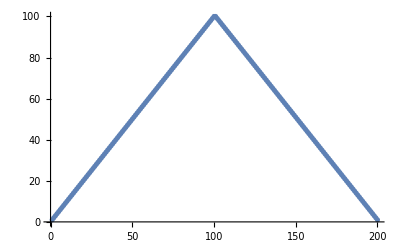

```mathematica
ListPlot[Join[Range[100],Reverse[Range[100]]]]
```

7. Используя функции Range и RandomInteger создайте список случайно генерированной длины, не превышающей число 10

```mathematica
Range[RandomInteger[10]]
```

{1,2,3,4,5}

8. Найти простейшую форму для команды Reverse[Reverse[Range[10]]]

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

9. Найти простейшую форму для команды Join[{1,2},Join[{3,4},{5}]]

```mathematica
Range[5]
```

{1,2,3,4,5}

10. Найти простейшую форму для команды Join[Range[10],Join[Range[10],Range[5]]]

```mathematica
Join[Range[10],Range[10],Range[5]]
```

{1,2,3,4,5,6,7,8,9,10,1,2,3,4,5,6,7,8,9,10,1,2,3,4,5}

11. Найти простейшую форму для команды Reverse[Join[Range[20],Reverse[Range[20]]]]

```mathematica
Join[Range[20],Reverse[Range[20]]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

```mathematica
3.1Use Range to create the list {1,2,3,4}.»
3.2Make a list of numbers up to 100. »
3.3Use Range and Reverse to create {4,3,2,1}.»
3.4Make a list of numbers from 1 to 50 in reverse order.»
3.5Use Range,Reverse and Join to create {1,2,3,4,4,3,2,1}.»
3.6Plot a list that counts up from 1 to 100,then down to 1. »
3.7Use Range and RandomInteger to make a list with a random length up to 10. »
3.8Find a simpler form for Reverse[Reverse[Range[10]]].»
3.9Find a simpler form for Join[{1,2},Join[{3,4},{5}]].»
3.10Find a simpler form for Join[Range[10],Join[Range[10],Range[5]]].»
3.11Find a simpler form for Reverse[Join[Range[20],Reverse[Range[20]]]].»
+3.1Compute the reverse of the reverse of {1,2,3,4}.»
+3.2Use Range,Reverse and Join to create the list {1,2,3,4,5,4,3,2,1}.»
+3.3Use Range,Reverse and Join to create {3,2,1,4,3,2,1,5,4,3,2,1}.»
+3.4Plot the list of numbers {10,11,12,13,14}.»
+3.5Find a simpler form for Join[Join[Range[10],Reverse[Range[10]]],Range[10]].»
```

#### I.2 Strings and Text

```mathematica
Text[Style["Строки и текст (Strings and Text)",24,Background->LightGreen]]
```

Строки и текст (Strings and Text)

1. Присоедините две копии строки «Здравствуйте».

```mathematica
StringJoin["Здравствуйте","Здравствуйте"]
```

ЗдравствуйтеЗдравствуйте

2. Создайте единую строку всего английского алфавита заглавными буквами.

```mathematica
ToUpperCase[Alphabet[]]
```

{A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W,X,Y,Z}

3. Сгенерируйте строку английского алфавита в обратном порядке.

```mathematica
Reverse[Alphabet[]]
```

{z,y,x,w,v,u,t,s,r,q,p,o,n,m,l,k,j,i,h,g,f,e,d,c,b,a}

4. Объедините 100 копий строки «ABCD»

```mathematica
Join[Table[ABCD,100]]
```

{ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD,ABCD}

5. Используйте StringTake, StringJoin и Alphabet, чтобы получить «abcdef»

```mathematica
StringTake[StringJoin[Alphabet[]],6]
```

abcdef

6. Создайте столбец с числом элементов, равных длине строки «это о строках» и содержащих число букв (включая пробелы) равное номеру элемента.

```mathematica
Column[Table[StringTake["это о строках",n],{n,StringLength["это о строках"]}]]
```

э
эт
это
это 
это о
это о 
это о с
это о ст
это о стр
это о стро
это о строк
это о строка
это о строках

7. Создайте гистограмму длин слов в «Давным-давно, в далекой галактике, далеко».

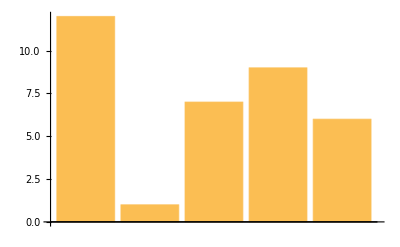

```mathematica
BarChart[StringLength[TextWords["Давным-давно, в далекой галактике, далеко"]]]
```

8. Найдите максимальную длину слова среди английских слов из WordList []

```mathematica
Max[StringLength[WordList[]]]
```

23

9. Используйте  Length, чтобы найти длину русского алфавита.

```mathematica
Length[Alphabet["Russian"]]
```

33

10. Создайте строку из заглавных букв греческого алфавита в обратном порядке.

```mathematica
ToUpperCase[StringJoin[Reverse[Alphabet["Greek"]]]]
```

ΩΨΧΦΥΤΣΡΠΟΞΝΜΛΚΙΘΗΖΕΔΓΒΑ

abcdefghijklmnopqrstuvwxyz

```mathematica
Text[Style["Чистые функции (Pure functions)",24,Background->LightGreen]]
```

Чистые функции (Pure functions)

#### I.3

1. Используйте Range и чистую функцию для создания списка из квадратов первых 20 натуральных чисел.

```mathematica
Power[#,2] & /@ {Range[20]}
```

{{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400}}

```mathematica
2^#
```

2. Составьте список из результатов смешивания желтого, зеленого и синего цветов с красным цветом.

```mathematica
Blend[{#,Red}] & /@ {Yellow,Green,Blue}
```

{RGBColor[1, Rational[1, 2], 0],RGBColor[Rational[1, 2], Rational[1, 2], 0],RGBColor[Rational[1, 2], 0, Rational[1, 2]]}

3. Создайте список  столбцов в рамках, содержащих прописные и строчные версии каждой буквы алфавита.

```mathematica
Framed[Column[{#, ToUpperCase[#]}]] & /@ Alphabet[]
```

{a
A,b
B,c
C,d
D,e
E,f
F,g
G,h
H,i
I,j
J,k
K,l
L,m
M,n
N,o
O,p
P,q
Q,r
R,s
S,t
T,u
U,v
V,w
W,x
X,y
Y,z
Z}

4.  Составьте список букв алфавита в случайных цветах в рамках, имеющих случайные цвета фона.

```mathematica
Style[Framed[Style[#,20, RandomColor[]]],Background->RandomColor[]] & /@ Alphabet[]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

5. Напишите в более простой форме команду (#^2+1&)/@Range[10].

```mathematica
Power[Range[10],2]+1
```

{2,5,10,17,26,37,50,65,82,101}

#### I.4

```mathematica
Text[Style["Композиции функций и их программирование",24,Background->LightGreen]]
```

Композиции функций и их программирование

1. Составьте список результатов использования функции Blur до 10 раз, начиная с растрированного размера 30 “X” (Используйте: Rasterize[Style).

```mathematica
NestList[Blur,Rasterize[Style["X",30]],10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

2. Начните с x, затем создайте список, использовав последовательно функцию Framed  до 10 раз, используя каждый раз случайный цвет фона.

```mathematica
NestList[Framed[#,Background->RandomColor[]]&,X,10]
```

{X,X,X,X,X,X,X,X,X,X,X}

3. Начните с размера 50 для "A", затем создайте список вложенного применения Framed и случайного вращения 5 раз.

```mathematica
NestList[Rotate[Framed[#],RandomReal[{0,360}]]&,Style["A",50],5]
```

{A,A,A,A,A,A}

4. Создайте линейный график из 100 итераций логического итерационного отображения 4 #(1-#)&, начиная с 0.2.

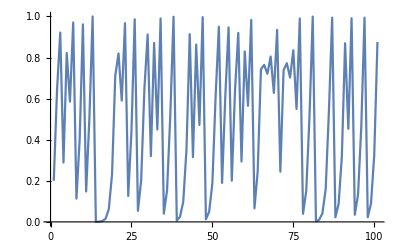

```mathematica
ListLinePlot[NestList[4 #(1-#)&,0.2,100]]
```

5. Найдите числовое значение результата из 30 итераций применения функции 1+1/#&, начиная с 1

```mathematica
NestList[1+1/# &,1,30]
```

{1,2,3/2,5/3,8/5,13/8,21/13,34/21,55/34,89/55,144/89,233/144,377/233,610/377,987/610,1597/987,2584/1597,4181/2584,6765/4181,10946/6765,17711/10946,28657/17711,46368/28657,75025/46368,121393/75025,196418/121393,317811/196418,514229/317811,832040/514229,1346269/832040,2178309/1346269}

6. Создайте список из первых 10 степеней 3 (начиная с 0) путем вложенного умножения.

```mathematica
NestList[3*#&,1,10]
```

{1,3,9,27,81,243,729,2187,6561,19683,59049}

7. Составьте список результатов действия вложенной функции (метод Ньютона) (# + 2 / #) / 2 до 5 раз, начиная с 1.0, а затем вычтите √2 из всех результатов.

```mathematica
NestList[(#+2/#)/2 &,1,5]-Sqrt[2]
```

{1-√2,3/2-√2,17/12-√2,577/408-√2,665857/470832-√2,886731088897/627013566048-√2}

8. Создайте список из 5 степеней числа 2, т. е. 2 ^ 2 ^ 2 ... ^ 2 n раз, причем n меняется от 0 до 4.

```mathematica
NestList[2^# &,1,4]
```

{1,2,4,16,65536}

#### I.5

```mathematica
Text[Style["Определение функций пользователя" ,20],Background->LightGreen]
```

Определение функций пользователя

1. Определите функцию f, которая вычисляет квадрат ее аргумента.

```mathematica
f[a_]:=a^2
```

4

2. Определите функцию poly, которая имеет целочисленное значение аргумента и создает изображение оранжевого правильного многоугольника с числом сторон, равным значению этого аргумента.

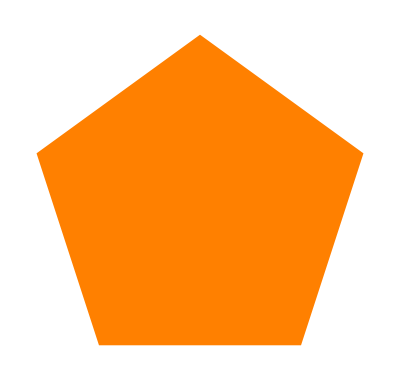

```mathematica
poly[a_Integer]:=Graphics[Style[RegularPolygon[a],Orange]]
```

3. Определите функцию f, которая берет список из двух элементов и помещает их в обратном порядке.

```mathematica
f[{a_,b_}]:={b,a}
```

{2,1}

4. Определите функцию f, которая имеет два аргумента и дает результат в виде дроби, где числитель равен произведению этих элементов, а знаменатель - их сумме.

```mathematica
f[a_,b_]:=(a*b)/(a+b)
```

6/5

5. Определите функцию f, которая имеет два аргумента и дает результат в виде списка трех элементов, которые соответственно равны сумме, разности и частному этих аргументов.

```mathematica
f[a_,b_]:={(a+b),(a-b),(a/b)}
```

{6,2,2}

6. Определите функцию evenodd, которая  зависит от одного целочисленного аргумента и имеет значение Black, если ее аргумент четный, значение - White в противном случае, значение Red - если аргумент равен нулю.

```mathematica
evenodd[a_Integer]:=If[EvenQ[a],Black,White,Red]
```

RGBColor[1, 0, 0]

7. Определите функцию Fibonacci f с f [0]=1 и f [1]=1, а f [n] для натурального числа n является суммой f [n-1] и f [n-2].

```mathematica
f[0]=f[1]=1;f[n_Integer]:=f[n-1]+f[n-2]
```

5